## Figure 10: Complexity

## Importing Data on Complexity

```mathematica
SetDirectory["/Users/claudius/work-claudius/general/paper-projects/repos/disintegrating-europe"]
```

/Users/claudius/work-claudius/general/paper-projects/repos/disintegrating-europe

```mathematica
"/Users/claudius/work-claudius/general/paper-projects/repos/disintegrating-europe"
```

/Users/claudius/work-claudius/general/paper-projects/repos/disintegrating-europe

```mathematica
data1=Import["data/wls_95_99_vs_03_07.csv"];
data2=Import["data/wls_03_07_vs_10_14.csv"];
data3=Import["data/wls_95_99_vs_10_14.csv"];
w1=Select[data1,#[[3]]=="long"&][[All,{1,12}]]
w2=Select[data2,#[[3]]=="long"&][[All,{1,12}]]
w3=Select[data3,#[[3]]=="long"&][[All,{1,12}]]
tradedata=Import["data/harv_eci_ranking.csv"];
tradeds=Dataset[AssociationThread[First@tradedata->#]&/@Rest@tradedata];
```

{{AUT,0.448086},{BEL,0.277379},{DEU,0.741143},{ESP,0.631343},{FIN,0.302787},{FRA,0.520982},{GRC,-0.263384},{IRL,1.37796},{ITA,0.216925},{NLD,-0.253876},{PRT,0.276972},{RdW,-0.478944}}

{{AUT,0.434257},{BEL,0.317802},{DEU,0.745139},{ESP,0.625633},{FIN,0.154657},{FRA,0.459184},{GRC,-0.489145},{IRL,1.36804},{ITA,0.171987},{NLD,-0.150294},{PRT,0.134228},{RdW,-0.405252}}

{{AUT,0.299962},{BEL,-0.123382},{DEU,0.614127},{ESP,0.26731},{FIN,-0.246687},{FRA,0.303664},{GRC,-1.41055},{IRL,1.66021},{ITA,0.133142},{NLD,-0.552011},{PRT,-0.0815244},{RdW,-0.592513}}

```mathematica
tradeds
```

Dataset[<>]

```mathematica
cof1={"AUT","BEL","BGR","CYP","CZE","DEU","DNK","ESP","EST","FIN","FRA","GRC","HUN","IRL","ITA","LTU","LVA","MLT","NLD","POL","PRT","ROU","SVK","SVN","SWE"};
cof2={"Austria","Belgium","Bulgaria","Cyprus","Czech Republic","Germany","Denmark","Spain","Estonia","Finland","France","Greece", "Hungary", "Ireland","Italy","Lithuania", "Latvia" ,"Malta","Netherlands", "Poland","Portugal","Romania","Slovakia","Slovenia", "Sweden"};
```

## Cleaning Data

```mathematica
core={"AUT","BEL","DEU","FIN","NLD"};
periplusFRA={"ESP","FRA","GRC", "IRL","ITA","PRT"};
coreperiplusFRA={core, periplusFRA};
eastern={"BGR","CZE","EST","HUN","LTU","LVA","POL","ROU","SVK","SVN"};
others={"CYP","MLT", "DNK", "SWE"};
allgroups={core,periplusFRA,eastern,others};
```

```mathematica
(*gives changes and complexity ranks for both periods*)
```

```mathematica
Keys[tradeds]
```

Dataset[<>]

```mathematica
plotdata1=Table[Append[Flatten[Cases[w1,{_?(#==cof1[[k]]&),_}]],Flatten[Values[Normal[tradeds[Select[#year==1999&&#locationcode==cof1[[k]]&],{"locationcode","year","complexity_harv_rank_simple"}]]]][[3]]],{k,1,Length[cof1]}];
plotdatagroups1={Cases[plotdata1,{_?(MemberQ[core,#]==True&),_,_}],Cases[plotdata1,{_?(MemberQ[periplusFRA,#]==True&),_,_}]};
```

```mathematica
plotdata2=Table[Append[Flatten[Cases[w2,{_?(#==cof1[[k]]&),_}]],Flatten[Values[Normal[tradeds[Select[#year==2007&&#locationcode==cof1[[k]]&],{"locationcode","year","complexity_harv_rank_simple"}]]]][[3]]],{k,1,Length[cof1]}];
plotdatagroups2={Cases[plotdata2,{_?(MemberQ[core,#]==True&),_,_}],Cases[plotdata2,{_?(MemberQ[periplusFRA,#]==True&),_,_}]};
```

```mathematica
plotdatagroups2
```

{{{AUT,0.434257,7},{BEL,0.317802,23},{DEU,0.745139,2},{FIN,0.154657,5},{NLD,-0.150294,34}},{{ESP,0.625633,47},{FRA,0.459184,16},{GRC,-0.489145,105},{IRL,1.36804,19},{ITA,0.171987,26},{PRT,0.134228,81}}}

```mathematica
plotdatagroups1
```

{{{AUT,0.448086,9},{BEL,0.277379,14},{DEU,0.741143,2},{FIN,0.302787,5},{NLD,-0.253876,24}},{{ESP,0.631343,33},{FRA,0.520982,10},{GRC,-0.263384,89},{IRL,1.37796,12},{ITA,0.216925,16},{PRT,0.276972,78}}}

```mathematica
w2
```

{{AUT,0.434257},{BEL,0.317802},{DEU,0.745139},{ESP,0.625633},{FIN,0.154657},{FRA,0.459184},{GRC,-0.489145},{IRL,1.36804},{ITA,0.171987},{NLD,-0.150294},{PRT,0.134228},{RdW,-0.405252}}

```mathematica
(*integrated data for both periods*)
```

```mathematica
joinforces2=Table[Labeled[Reverse[plotdatagroups1[[g,k,2;;3]]],plotdatagroups1[[g,k,1]]],{g,1,2},{k,1,Length[coreperiplusFRA[[g]]]}]~Join~Table[Labeled[Reverse[plotdatagroups2[[g,k,2;;3]]],plotdatagroups2[[g,k,1]]],{g,1,2},{k,1,Length[coreperiplusFRA[[g]]]}]
```

{{{9,0.448086}AUT,{14,0.277379}BEL,{2,0.741143}DEU,{5,0.302787}FIN,{24,-0.253876}NLD},{{33,0.631343}ESP,{10,0.520982}FRA,{89,-0.263384}GRC,{12,1.37796}IRL,{16,0.216925}ITA,{78,0.276972}PRT},{{7,0.434257}AUT,{23,0.317802}BEL,{2,0.745139}DEU,{5,0.154657}FIN,{34,-0.150294}NLD},{{47,0.625633}ESP,{16,0.459184}FRA,{105,-0.489145}GRC,{19,1.36804}IRL,{26,0.171987}ITA,{81,0.134228}PRT}}

```mathematica
Dimensions[joinforces2]
```

{4}

## Generating Figure 10

### Regression Line for 10 (a)

```mathematica
regdata1=Flatten[joinforces2[[All, All,1]][[1;;2]],1];
regdata2=Flatten[joinforces2[[All, All,1]][[3;;4]],1];
linepooled=Fit[Join[regdata1,regdata2],{1,comprank},comprank]
```

0.60384-0.00797059 comprank

```mathematica
lmpooled=LinearModelFit[Join[regdata1,regdata2],{comprank},{comprank}]
lmpooled[{"ParameterTable","RSquared"}]
```

FittedModel[0.60384-0.00797059 comprank]

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.60384 | 0.120494 | 5.01138 | 0.0000669564
comprank | -0.00797059 | 0.00284991 | -2.79679 | 0.0111359,0.281145}

### Reformatting data for 10(a)

```mathematica
directeddata=Table[{joinforces2[[All,All,1]][[1,k]],joinforces2[[All,All,1]][[3,k]]},{k,1,5}]~Join~Table[{joinforces2[[All,All,1]][[2,k]],joinforces2[[All,All,1]][[4,k]]},{k,1,6}]
```

{{{9,0.448086},{7,0.434257}},{{14,0.277379},{23,0.317802}},{{2,0.741143},{2,0.745139}},{{5,0.302787},{5,0.154657}},{{24,-0.253876},{34,-0.150294}},{{33,0.631343},{47,0.625633}},{{10,0.520982},{16,0.459184}},{{89,-0.263384},{105,-0.489145}},{{12,1.37796},{19,1.36804}},{{16,0.216925},{26,0.171987}},{{78,0.276972},{81,0.134228}}}

```mathematica
directeddata2=Table[{joinforces2[[All,All,1]][[1,k]],Labeled[joinforces2[[All,All,1]][[3,k]],core[[k]]]},{k,1,5}]~Join~Table[{joinforces2[[All,All,1]][[2,k]],Labeled[joinforces2[[All,All,1]][[4,k]],periplusFRA[[k]]]},{k,1,6}]
```

{{{9,0.448086},{7,0.434257}AUT},{{14,0.277379},{23,0.317802}BEL},{{2,0.741143},{2,0.745139}DEU},{{5,0.302787},{5,0.154657}FIN},{{24,-0.253876},{34,-0.150294}NLD},{{33,0.631343},{47,0.625633}ESP},{{10,0.520982},{16,0.459184}FRA},{{89,-0.263384},{105,-0.489145}GRC},{{12,1.37796},{19,1.36804}IRL},{{16,0.216925},{26,0.171987}ITA},{{78,0.276972},{81,0.134228}PRT}}

```mathematica
legend=Grid[{{Graphics[{Purple,Disk[{0,0},0.1]},ImageSize->7],Style["Core",FontFamily->"Myriad Pro",12]},{Graphics[{Orange,Disk[{0,0},0.1]},ImageSize->7],Style["Periphery",FontFamily->"Myriad Pro",12]}},BaselinePosition->Bottom,Alignment->Left,Spacings->{0.3,.5}]
```

-Graphics- | Core
-Graphics- | Periphery

### Final Act

```mathematica
FIG10A=Show[ListPlot[directeddata,Frame->True,GridLines->{None,{-0.5,-0.25,0,0.25,0.5,0.75,1,1.25,1.5}},PlotMarkers->•,ImageSize->Large,FrameStyle->Black, Joined->True,PlotStyle->Join[Table[{Purple,Thickness[0.0015],Arrowheads[{0.02}]},{5}],{{Orange,Thickness[0.0015],Arrowheads[{0.02}]}},{{Darker[Green],Thickness[0.0015],Arrowheads[{0.02}]}},Table[{Orange,Thickness[0.0015],Arrowheads[{0.02}]},{4}]],LabelStyle->{FontFamily->"Myriad Pro",12},PlotLegends->legend,FrameLabel->{{Row[{Style["directedness of technological change:\n ",Bold],"average complexity of growing and declining sectors \n (1995-99 vs. 2003-07 and 2003-07 vs. 2010-14)"}],None},{Row[{Style["initial position:\n ",Bold],"complexity rank in starting year (1999/2007)"}],None}},PlotLabel-> Style["Technological capabilities and sectoral change",Black,14],
Epilog->{Locator[{4,0.425},"AUT"],
Locator[{68,-0.14},Style["Linear regression:
0.6 - 0.008 comprank^(**), R^2=0.28",FontFamily->"Myriad Pro",FontSize->11, Gray,TextAlignment->Left]]}]/.Line->Arrow,
Plot[linepooled,{comprank,0,120},PlotStyle->{Gray,Thickness[.002]}],ListPlot[directeddata2]]
```

-Graphics-

```mathematica
Export["output/fig_10a_tech-change.pdf",FIG10A]
```

output/fig_10a_tech-change.pdf

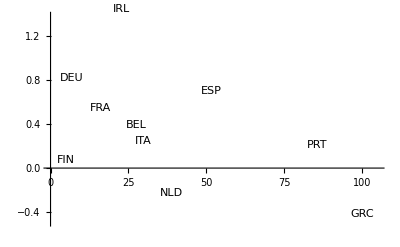

```mathematica
ListPlot[directeddata2]
```

### Reformatting data for 10(b)

```mathematica
plotdatanew1=Table[Reverse[plotdatagroups1[[g,k,2;;3]]],{g,1,2},{k,1,Length[allgroups[[g]]]}];
plotdatanew2=Table[Reverse[plotdatagroups2[[g,k,2;;3]]],{g,1,2},{k,1,Length[allgroups[[g]]]}];
joinforcesforaverage=(plotdatanew2-plotdatanew1)*{Table[{-1,1},{5}],Table[{-1,1},{6}]};
plotlines1=Table[{{0,0},joinforcesforaverage[[k,l]]},{k,1,2},{l,1,If[k==1,5,6]}];
starplotdatalabel=Table[Labeled[Join[plotlines1[[1]],plotlines1[[2]]][[k]],Flatten[joinforces2[[All,All,2]][[1;;2]]][[k]],{Below,Above,Above,Bottom,Bottom,Left,Above,Above,Above,Bottom,Right}[[k]]],{k,1,11}]
starplotdata=Table[Join[plotlines1[[1]],plotlines1[[2]]][[k]],{k,1,11}]
```

{Labeled[{{0,0},{2,-0.013829}},AUT,Below],Labeled[{{0,0},{-9,0.0404233}},BEL,Above],Labeled[{{0,0},{0,0.0039952}},DEU,Above],{{0,0},{0,-0.148131}}FIN,{{0,0},{-10,0.103582}}NLD,{{0,0},{-14,-0.00571027}}ESP,Labeled[{{0,0},{-6,-0.061798}},FRA,Above],Labeled[{{0,0},{-16,-0.225761}},GRC,Above],Labeled[{{0,0},{-7,-0.0099139}},IRL,Above],{{0,0},{-10,-0.0449374}}ITA,{{0,0},{-3,-0.142743}}PRT}

{{{0,0},{2,-0.013829}},{{0,0},{-9,0.0404233}},{{0,0},{0,0.0039952}},{{0,0},{0,-0.148131}},{{0,0},{-10,0.103582}},{{0,0},{-14,-0.00571027}},{{0,0},{-6,-0.061798}},{{0,0},{-16,-0.225761}},{{0,0},{-7,-0.0099139}},{{0,0},{-10,-0.0449374}},{{0,0},{-3,-0.142743}}}

```mathematica
plotlines1L=Flatten[Table[{{0,0},Labeled[joinforcesforaverage[[k,l]],Join[core,periplusFRA][[If[k==1,l,l+5]]],Background->None]},{k,1,2},{l,1,If[k==1,5,6]}],1]
```

{{{0,0},{2,-0.013829}AUT},{{0,0},{-9,0.0404233}BEL},{{0,0},{0,0.0039952}DEU},{{0,0},{0,-0.148131}FIN},{{0,0},{-10,0.103582}NLD},{{0,0},{-14,-0.00571027}ESP},{{0,0},{-6,-0.061798}FRA},{{0,0},{-16,-0.225761}GRC},{{0,0},{-7,-0.0099139}IRL},{{0,0},{-10,-0.0449374}ITA},{{0,0},{-3,-0.142743}PRT}}

```mathematica
starplotdata=Table[Join[plotlines1[[1]],plotlines1[[2]]][[k]],{k,1,11}]
```

{{{0,0},{2,-0.013829}},{{0,0},{-9,0.0404233}},{{0,0},{0,0.0039952}},{{0,0},{0,-0.148131}},{{0,0},{-10,0.103582}},{{0,0},{-14,-0.00571027}},{{0,0},{-6,-0.061798}},{{0,0},{-16,-0.225761}},{{0,0},{-7,-0.0099139}},{{0,0},{-10,-0.0449374}},{{0,0},{-3,-0.142743}}}

```mathematica
starplotdata2=Table[Labeled[starplotdata[[All,2]][[k]],Join[core,periplusFRA][[k]],Background->None],{k,1,Length[starplotdata]}]
```

{{2,-0.013829}AUT,{-9,0.0404233}BEL,{0,0.0039952}DEU,{0,-0.148131}FIN,{-10,0.103582}NLD,{-14,-0.00571027}ESP,{-6,-0.061798}FRA,{-16,-0.225761}GRC,{-7,-0.0099139}IRL,{-10,-0.0449374}ITA,{-3,-0.142743}PRT}

### Final Act

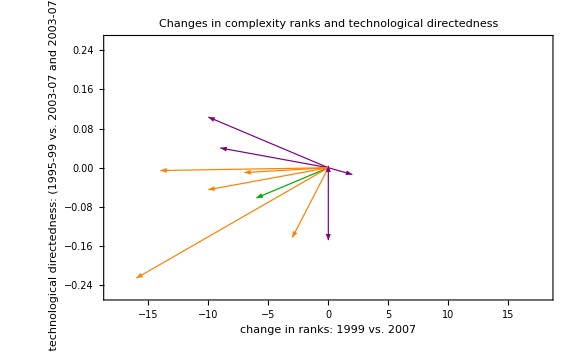

```mathematica
FIG10bpart1=ListPlot[starplotdata,Joined->True,PlotRange->{{-18,18},{-0.26,0.26}},Frame->True,ImageSize->Large,FrameStyle->Black,FrameLabel->{{Row[{Style["change in technological directedness:\n ",Bold],"(1995-99 vs. 2003-07 and 2003-07 vs. 2010-14)"}],None},{Row[{Style["change in ranks:\n ",Bold],"1999 vs. 2007"}],None}},PlotLabel-> Style["Changes in complexity ranks and technological directedness",Black,14],LabelStyle->{FontFamily->"Myriad Pro",12},PlotStyle->Join[Table[{Purple,Thickness[0.0015],Arrowheads[{0.022}]},{2}],{{Purple,Thickness[0.0015],Arrowheads[{0.002}]}},Table[{Purple,Thickness[0.0015],Arrowheads[{0.022}]},{2}],{{Orange,Thickness[0.0015],Arrowheads[{0.022}]}},{{Darker[Green],Thickness[0.0015],Arrowheads[{0.022}]}},Table[{Orange,Thickness[0.0015],Arrowheads[{0.022}]},{4}]]]/.Line->Arrow
```

```mathematica
+
```

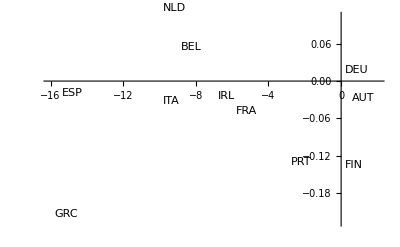

```mathematica
FIG10bpart1a=ListPlot[plotlines1L,PlotRange->Full]
```

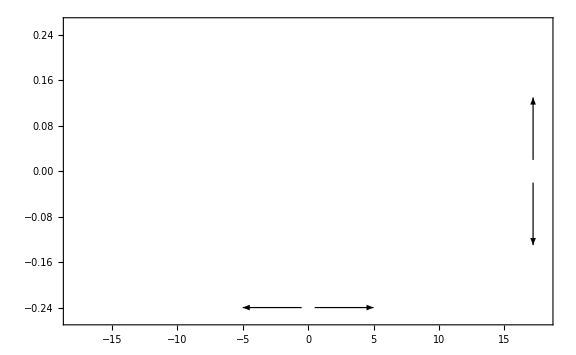

```mathematica
FIG10bpart2=ListPlot[{{{0.5,-0.24},{5,-0.24}}, {{-0.5,-0.24},{-5,-0.24}},{{17.2,-0.02},{17.2,-0.13}},{{17.2,0.02},{17.2,0.13}}},PlotRange->{{-18,18},{-0.26,0.26}},Joined->True,PlotStyle->{{Black,Thickness[0.0015],Arrowheads[{0.022}]}},ImageSize->Large,Frame->True]/.Line->Arrow
```

```mathematica
FIG10bpart3=ListPlot[{{0,0},{-18,0}},PlotRange->{{-18,18},{-0.26,0.26}},Joined->True,Filling->Bottom,PlotStyle->{Orange,Thickness->.000000000000000000000000000000000001},FillingStyle->Directive[Opacity[0.1]],ImageSize->Large];
FIG10bpart4=ListPlot[{{-18,0},{0,0},{0,-0.26},{18,-0.26}},PlotRange->{{-18,18},{-0.26,0.26}},Joined->True,Filling->Top,PlotStyle->{Purple,Thickness->.00000000000000000000001},FillingStyle->Directive[Opacity[0.1]],ImageSize->Large];
```

```mathematica
FIG10B=Show[FIG10bpart1,FIG10bpart1a,FIG10bpart3,FIG10bpart4,FIG10bpart2,Epilog->{Locator[{5.6,-0.22},Style["improvement in ranking",FontFamily->"Myriad Pro",12]],Locator[{-4.7,-0.22},Style["decrease in ranking",FontFamily->"Myriad Pro",12]],Locator[{11.3,0.16},Style["positive tendency\n in technological development" ,FontFamily->"Myriad Pro",12,TextAlignment->Right]],Locator[{11.3,-0.16},Style["negative tendency\n in technological development" ,FontFamily->"Myriad Pro",12,TextAlignment->Right]]}]
```

-Graphics-

```mathematica
Export["output/fig_10b_tech-change.pdf",FIG10B]
```

output/fig_10b_tech-change.pdf